```mathematica
eq1=4*α*x*(1-x)+β*y*(1-x);
eq2=4*α*y*(1-y)+β*x*(1-y);
```

```mathematica
zeros1=FullSimplify[Solve[{eq1-x==0,eq2-y==0},{x,y}]]/.{β->0.5};
```

```mathematica
zeros11=zeros1[[1]];
zeros12=zeros1[[2]];
zeros13=zeros1[[3]];
zeros14=zeros1[[4]];
```

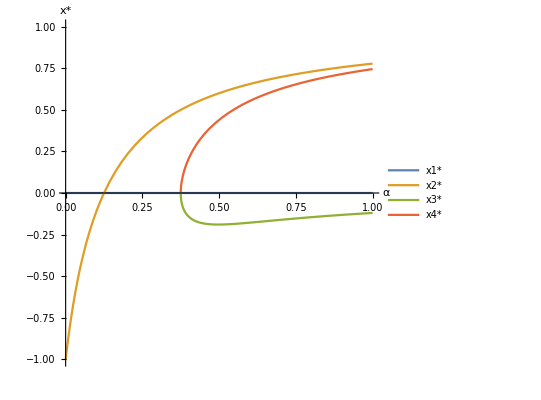

```mathematica
Plot[
{zeros11[[1]][[2]],
zeros12[[1]][[2]],
zeros13[[1]][[2]],
zeros14[[1]][[2]]},
{α,0,1},
AxesLabel->{
Style["α",FontSize->16,FontWeight->Bold],
Style["x*",FontSize->16,FontWeight->Bold]
},
PlotStyle->{"Red","Blue","Green","Brown"},
AspectRatio->1,
PlotRange->{{0,1},{-1,1}},
PlotLegends->{"x1*","x2*","x3*","x4*"}
]
```

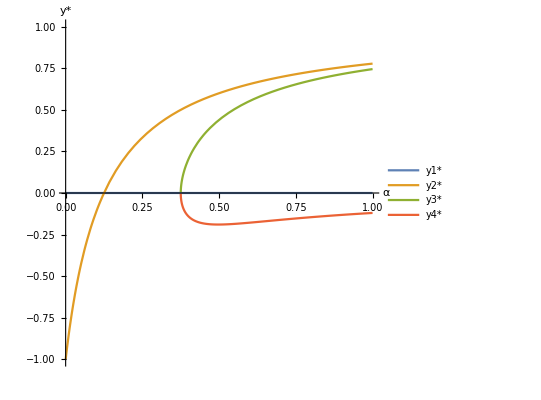

```mathematica
Plot[
{zeros11[[2]][[2]],
zeros12[[2]][[2]],
zeros13[[2]][[2]],
zeros14[[2]][[2]]},
{α,0,1},
AxesLabel->{
Style["α",FontSize->16,FontWeight->Bold],
Style["y*",FontSize->16,FontWeight->Bold]
},
PlotStyle->{"Red","Blue","Green","Brown"},
AspectRatio->1,
PlotRange->{{0,1},{-1,1}},
PlotLegends->{"y1*","y2*","y3*","y4*"}
]
```

```mathematica
Jac={{D[eq1,x],D[eq1,y]},{D[eq2,x],D[eq2,y]}}/.{β->0.5};
MatrixForm[Jac]
```

(-0.5 y+4 (1-x) α-4 x α | 0.5 (1-x)
0.5 (1-y) | -0.5 x+4 (1-y) α-4 y α)

```mathematica
zeros11
zeros12
zeros13
zeros14
```

{x→0,y→0}

{x→1-1/(0.5+4 α),y→1-1/(0.5+4 α)}

{x→(1. (1.5-4 α))/(0.75-4. α+4 α (-1+4 α)+√((-1.5+4 α) (-0.5+4 α) (0.75+4. α+4 α (-1+4 α)))),y→(1. (1.5-4 α))/(0.75-4. α+4 α (-1+4 α)-√((-1.5+4 α) (-0.5+4 α) (0.75+4. α+4 α (-1+4 α))))}

{x→(1. (1.5-4 α))/(0.75-4. α+4 α (-1+4 α)-√((-1.5+4 α) (-0.5+4 α) (0.75+4. α+4 α (-1+4 α)))),y→(1. (1.5-4 α))/(0.75-4. α+4 α (-1+4 α)+√((-1.5+4 α) (-0.5+4 α) (0.75+4. α+4 α (-1+4 α))))}

```mathematica
Jac11=FullSimplify[Jac/.zeros11];
Jac12=FullSimplify[Jac/.zeros12];
Jac13=FullSimplify[Jac/.zeros13];
Jac14=FullSimplify[Jac/.zeros14];
```

```mathematica
Lambda11=FullSimplify[Eigenvalues[Jac11]]
Lambda12=FullSimplify[Eigenvalues[Jac12]]
Lambda13=FullSimplify[Eigenvalues[Jac13]]
Lambda14=FullSimplify[Eigenvalues[Jac14]]
```

{-0.5+4. α,0.5+4. α}

{1.5-4. α-0.25/(0.125+1. α),1.5-4. α}

{(0.5 α (18.-96. α-2560. α^2+22528. α^3-40960. α^4-131072. (0.125-1. α)^2 (-0.362879+1. α)^(3/2) √(-0.0419162+1. α) √(0.0386997+α (0.00555189+1. α))))/(0.+96. α^2-1792. α^3+10240. α^4-16384. α^5),(0.5 α (18.-96. α-2560. α^2+22528. α^3-40960. α^4+131072. (0.125-1. α)^2 (-0.362879+1. α)^(3/2) √(-0.0419162+1. α) √(0.0386997+α (0.00555189+1. α))))/(0.+96. α^2-1792. α^3+10240. α^4-16384. α^5)}

{(0.5 α (18.-96. α-2560. α^2+22528. α^3-40960. α^4-131072. (0.125-1. α)^2 (-0.362879+1. α)^(3/2) √(-0.0419162+1. α) √(0.0386997+α (0.00555189+1. α))))/(0.+96. α^2-1792. α^3+10240. α^4-16384. α^5),(0.5 α (18.-96. α-2560. α^2+22528. α^3-40960. α^4+131072. (0.125-1. α)^2 (-0.362879+1. α)^(3/2) √(-0.0419162+1. α) √(0.0386997+α (0.00555189+1. α))))/(0.+96. α^2-1792. α^3+10240. α^4-16384. α^5)}

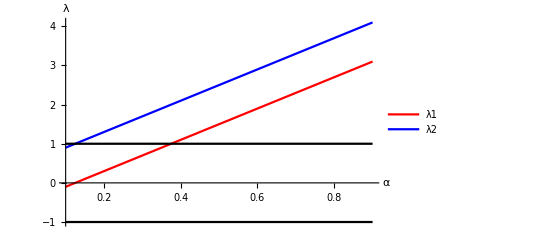

```mathematica
Plot[
{Lambda11,
-1,
1},
{α,0.1,0.9},
PlotStyle->{Red,Blue,Black,Black},
AxesLabel->{
Style["α",FontSize->14,FontColor->Black],
Style["λ",FontSize->14,FontColor->Black]},
PlotLegends->{"λ1","λ2"}
]
```

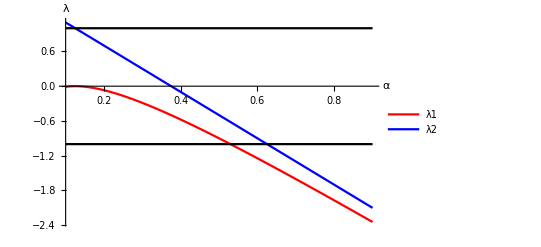

```mathematica
Plot[
{Lambda12,
-1,
1},
{α,0.1,0.9},
PlotStyle->{Red,Blue,Black,Black},
AxesLabel->{
Style["α",FontSize->14,FontColor->Black],
Style["λ",FontSize->14,FontColor->Black]},
PlotLegends->{"λ1","λ2"}
]
```

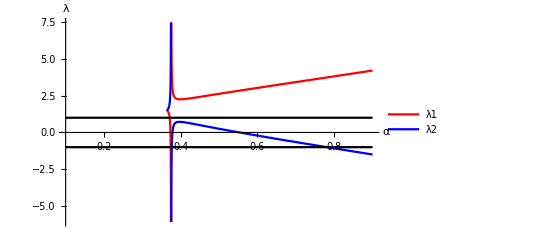

```mathematica
Plot[
{Lambda13,
-1,
1},
{α,0.1,0.9},
PlotStyle->{Red,Blue,Black,Black},
AxesLabel->{
Style["α",FontSize->14,FontColor->Black],
Style["λ",FontSize->14,FontColor->Black]},
PlotLegends->{"λ1","λ2"}
]
```

```mathematica
Plot[
{Lambda14,
-1,
1},
{α,0.1,0.9},
PlotStyle->{Red,Blue,Black,Black},
AxesLabel->{
Style["α",FontSize->14,FontColor->Black],
Style["λ",FontSize->14,FontColor->Black]},
PlotLegends->{"λ1","λ2"}
]
```

-Graphics-

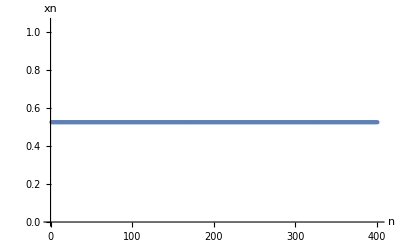

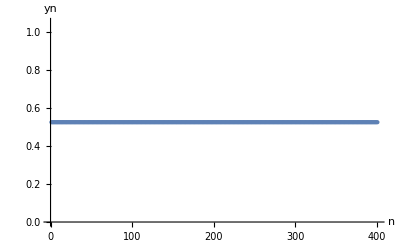

```mathematica
xn=RandomReal[];
yn=RandomReal[];

F1[x_,y_]:=(4*α*x+β*y)*(1-x)/.{α->0.4,β->0.5};
F2[x_,y_]:=(4*α*y+β*x)*(1-y)/.{α->0.4,β->0.5};

Nit= 500;
Ntransient=100;
xv={xn};
yv={yn};
Do[
xn1=F1[xn,yn];
yn1=F2[xn,yn];
AppendTo[xv,xn];
AppendTo[yv,yn];
xn=xn1;
yn=yn1,
{i, Nit}
]
xvsteady=Rest[xv[[Ntransient;;]]];
yvsteady=Rest[yv[[Ntransient;;]]];

ListPlot[
xvsteady,
AxesLabel->{
Style["n",FontSize->14,FontColor->Black],
Style["xn",FontSize->14,FontColor->Black]}]
ListPlot[
yvsteady,
AxesLabel->{
Style["n",FontSize->14,FontColor->Black],
Style["yn",FontSize->14,FontColor->Black]}]
```